```mathematica
<<MaTeX`
texStyle={FontFamily->"CMU serif",FontSize->12};
```

```mathematica
ClearAll[chi]
chi[t_,X_,Y_]:={X+t X^2,Y+t X Y}
chi3[t_,X_,Y_,Z_]:=Join[chi[t,X,Y],{Z}]
```

```mathematica
J=Det[Grad[chi3[t,X,Y,Z],{X,Y,Z}]]
```

(1+t X) (1+2 t X)

```mathematica
Solve[chi[t,X,Y]=={x,y},{X,Y}]
tosmall=Last@Solve[chi[t,X,Y]=={x,y},{X,Y}];
{X,Y}/. tosmall//FullSimplify// TeXForm
```

{{X→(-1-√(1+4 t x))/(2 t),Y→(-y/t-(√(1+4 t x) y)/t)/(2 x)},{X→(-1+√(1+4 t x))/(2 t),Y→(-y/t+(√(1+4 t x) y)/t)/(2 x)}}

\left\{\frac{\sqrt{4 t x+1}-1}{2 t},\frac{y \left(\sqrt{4 t x+1}-1\right)}{2 t x}\right\}

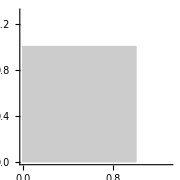
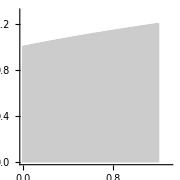

../images/gibanje0.pdf

../images/gibanje02.pdf

```mathematica
pl1=ParametricPlot[chi[0,X,Y],{X,0,1},{Y,0,1},
PlotRange->{{0,1.3},{0,1.3}},
Frame->False,
BaseStyle->texStyle,
AxesLabel->{MaTeX["X"],MaTeX["Y"]},
AxesStyle->Black,
ImageSize->Small,
ColorFunction->(GrayLevel[0.8]&),
BoundaryStyle->Black,
Mesh->Full,
MeshStyle->Black
];
pl2=ParametricPlot[chi[0.2,X,Y],{X,0,1},{Y,0,1},
PlotRange->{{0,1.3},{0,1.3}},
Frame->False,
BaseStyle->texStyle,
AxesLabel->{MaTeX["X"],MaTeX["Y"]},
AxesStyle->Black,
ImageSize->Small,
ColorFunction->(GrayLevel[0.8]&),
BoundaryStyle->Black,
Mesh->Full,
MeshStyle->Black
];
Row[{pl1,pl2}]
Export["../images/gibanje0.pdf",pl1]
Export["../images/gibanje02.pdf",pl2]
```

```mathematica
theta = t X^2+2 Z Y
tsmall=theta /.tosmall /.{Z->z}// FullSimplify
```

t X^2+2 Y Z

(x+2 t x^2-x √(1+4 t x)+2 (-1+√(1+4 t x)) y z)/(2 t x)

```mathematica
D[tsmall,y]//Simplify//TeXForm
```

\frac{z \left(\sqrt{4 t x+1}-1\right)}{t x}

```mathematica
theta /.
```

```mathematica
D[tsmall,t] // Simplify // TeXForm
```

-\frac{\left(-2 t x+\sqrt{4 t x+1}-1\right) (x-2 y z)}{2 t^2 x \sqrt{4 t x+1}}

```mathematica
gibanje = {x[t,X,Y,Z],y[t,X,Y,Z],z[t,X,Y,Z]};
F = Grad[gibanje,{X,Y,Z}]
J=Det[F]
```

{{x^(0,1,0,0)[t,X,Y,Z],x^(0,0,1,0)[t,X,Y,Z],x^(0,0,0,1)[t,X,Y,Z]},{y^(0,1,0,0)[t,X,Y,Z],y^(0,0,1,0)[t,X,Y,Z],y^(0,0,0,1)[t,X,Y,Z]},{z^(0,1,0,0)[t,X,Y,Z],z^(0,0,1,0)[t,X,Y,Z],z^(0,0,0,1)[t,X,Y,Z]}}

z^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z]-y^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z]-z^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z]+x^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z]+y^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z]-x^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z]

```mathematica
D[J,t]
```

z^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] x^(1,0,0,1)[t,X,Y,Z]-y^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] x^(1,0,0,1)[t,X,Y,Z]-z^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] y^(1,0,0,1)[t,X,Y,Z]+x^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] y^(1,0,0,1)[t,X,Y,Z]+y^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] z^(1,0,0,1)[t,X,Y,Z]-x^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] z^(1,0,0,1)[t,X,Y,Z]-z^(0,0,0,1)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] x^(1,0,1,0)[t,X,Y,Z]+y^(0,0,0,1)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] x^(1,0,1,0)[t,X,Y,Z]+z^(0,0,0,1)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] y^(1,0,1,0)[t,X,Y,Z]-x^(0,0,0,1)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] y^(1,0,1,0)[t,X,Y,Z]-y^(0,0,0,1)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] z^(1,0,1,0)[t,X,Y,Z]+x^(0,0,0,1)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] z^(1,0,1,0)[t,X,Y,Z]+z^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] x^(1,1,0,0)[t,X,Y,Z]-y^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] x^(1,1,0,0)[t,X,Y,Z]-z^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] y^(1,1,0,0)[t,X,Y,Z]+x^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] y^(1,1,0,0)[t,X,Y,Z]+y^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] z^(1,1,0,0)[t,X,Y,Z]-x^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] z^(1,1,0,0)[t,X,Y,Z]

```mathematica
J Div[D[gibanje,t],{X,Y,Z}]//Expand
```

z^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] z^(1,0,0,1)[t,X,Y,Z]-y^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] z^(1,0,0,1)[t,X,Y,Z]-z^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] z^(1,0,0,1)[t,X,Y,Z]+x^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] z^(1,0,0,1)[t,X,Y,Z]+y^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] z^(1,0,0,1)[t,X,Y,Z]-x^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] z^(1,0,0,1)[t,X,Y,Z]+z^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] y^(1,0,1,0)[t,X,Y,Z]-y^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] y^(1,0,1,0)[t,X,Y,Z]-z^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] y^(1,0,1,0)[t,X,Y,Z]+x^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] y^(1,0,1,0)[t,X,Y,Z]+y^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] y^(1,0,1,0)[t,X,Y,Z]-x^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] y^(1,0,1,0)[t,X,Y,Z]+z^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] x^(1,1,0,0)[t,X,Y,Z]-y^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] x^(0,1,0,0)[t,X,Y,Z] x^(1,1,0,0)[t,X,Y,Z]-z^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] x^(1,1,0,0)[t,X,Y,Z]+x^(0,0,0,1)[t,X,Y,Z] z^(0,0,1,0)[t,X,Y,Z] y^(0,1,0,0)[t,X,Y,Z] x^(1,1,0,0)[t,X,Y,Z]+y^(0,0,0,1)[t,X,Y,Z] x^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] x^(1,1,0,0)[t,X,Y,Z]-x^(0,0,0,1)[t,X,Y,Z] y^(0,0,1,0)[t,X,Y,Z] z^(0,1,0,0)[t,X,Y,Z] x^(1,1,0,0)[t,X,Y,Z]

```mathematica
Det[{{a,b,c},{d,e,f},{g,h,i}}]
```

-c e g+b f g+c d h-a f h-b d i+a e i

```mathematica
V = D[chi3[t,X,Y,Z],t]
v = V/.tosmall // Simplify
```

{X^2,X Y,0}

{(-1+√(1+4 t x))^2/(4 t^2),((-1+√(1+4 t x))^2 y)/(4 t^2 x),0}

```mathematica
div=Div[v,{x,y,z}] // Simplify
```

-((-1+√(1+4 t x)) (-1-8 t x+√(1+4 t x)))/(4 t^2 x √(1+4 t x))

```mathematica
J = Det[Grad[chi3[t,X,Y,Z],{X,Y,Z}]]
j=J/.tosmall
```

(1+t X) (1+2 t X)

√(1+4 t x) (1+1/2 (-1+√(1+4 t x)))

```mathematica
(D[J,t]/.tosmall)==j div // FullSimplify
```

True